{cell_forces150.000000.gpl,cell_forces165.000000.gpl,cell_forces180.000000.gpl,cell_forces195.000000.gpl,cell_forces210.000000.gpl,cell_forces225.000000.gpl,cell_forces240.000000.gpl,cell_forces255.000000.gpl,cell_forces270.000000.gpl,cell_forces285.000000.gpl,cell_forces300.000000.gpl,cell_forces315.000000.gpl,cell_forces330.000000.gpl,cell_forces345.000000.gpl,cell_forces360.000000.gpl,cell_forces375.000000.gpl,cell_forces390.000000.gpl,cell_forces405.000000.gpl,cell_forces420.000000.gpl,cell_forces435.000000.gpl,cell_forces450.000000.gpl,cell_forces465.000000.gpl,cell_forces480.000000.gpl,cell_forces495.000000.gpl,cell_forces510.000000.gpl,cell_forces525.000000.gpl,cell_forces540.000000.gpl,cell_forces555.000000.gpl,cell_forces570.000000.gpl,cell_forces585.000000.gpl,cell_forces600.000000.gpl,cell_forces615.000000.gpl,cell_forces630.000000.gpl,cell_forces645.000000.gpl,cell_forces660.000000.gpl,cell_forces675.000000.gpl,cell_forces690.000000.gpl,cell_forces705.000000.gpl,cell_forces720.000000.gpl,cell_forces735.000000.gpl,cell_forces750.000000.gpl,cell_forces765.000000.gpl,cell_forces780.000000.gpl,cell_forces795.000000.gpl,cell_forces810.000000.gpl,cell_forces825.000000.gpl,cell_forces840.000000.gpl,cell_forces855.000000.gpl,cell_forces870.000000.gpl,cell_forces885.000000.gpl,cell_forces900.000000.gpl,cell_forces915.000000.gpl,cell_forces930.000000.gpl,cell_forces945.000000.gpl,cell_forces960.000000.gpl,cell_forces975.000000.gpl,cell_forces990.000000.gpl}

/home/kempsilonnaught/Builds/CellSurfaceFE/MongeParameterization/SimpleTwoInclusionLift

{{150,10986.7},{165,11199.5},{180,11312.1},{195,11468.1},{210,11645.7},{225,11821.2},{240,12000},{255,12148.8},{270,12272.7},{285,12448.1},{300,12594.9},{315,12717.7},{330,12847.3},{345,12980.9},{360,13065.7},{375,13193.9},{390,13281.6},{405,13391.8},{420,13469.7},{435,13549.7},{450,13665.9},{465,13733.2},{480,13806.7},{495,13892.3},{510,13969.6},{525,14105.4},{540,14182.4},{555,14239},{570,14312.5},{585,14400.9},{600,14465.7},{615,14501.9},{630,14564.5},{645,14638.1},{660,14708.5},{675,14744.5},{690,14799.5},{705,14842.4},{720,14893.9},{735,14962.1},{750,14992.9},{765,15025.1},{780,15080.3},{795,15105.3},{810,15147.2},{825,15182.3},{840,15205},{855,15269.1},{870,15265.1},{885,15299.6},{900,15355.2},{915,15368.2},{930,15388.2},{945,15418.5},{960,15438},{975,15471},{990,15501.4}}

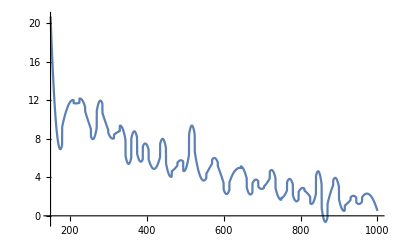

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE/MongeParameterization/SimpleTwoInclusionLift/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange -> All];
{plot1,plot2}
]
files= FileNames[]
(*Print[files]*)
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
]
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE/MongeParameterization/SimpleTwoInclusionLift"]
Print[SolveForce["energysep.txt"]]
energysepfunc = Interpolation[SolveForce["energysep.txt"]];
forcefunction = energysepfunc';
Plot[forcefunction[x], {x, 150, 1000}]
```

```mathematica
(*{{150,10986.7},{165,11199.5},{180,11312.1},{195,11468.1},{210,11645.7},{225,11821.2},{240,12000},{255,12148.8},{270,12272.7},{285,12448.1},{300,12594.9},{315,12717.7},{330,12847.3},{345,12980.9},{360,13065.7},{375,13193.9},{390,13281.6},{405,13391.8},{420,13469.7},{435,13549.7},{450,13665.9},{465,13733.2},{480,13806.7},{495,13892.3},{510,13969.6},{525,14105.4},{540,14182.4},{555,14239},{570,14312.5},{585,14400.9},{600,14465.7},{615,14501.9},{630,14564.5},{645,14638.1},{660,14708.5},{675,14744.5},{690,14799.5},{705,14842.4},{720,14893.9},{735,14962.1},{750,14992.9},{765,15025.1},{780,15080.3},{795,15105.3},{810,15147.2},{825,15182.3},{840,15205},{855,15269.1},{870,15265.1},{885,15299.6},{900,15355.2},{915,15368.2},{930,15388.2},{945,15418.5},{960,15438},{975,15471},{990,15501.4}}*)
```